```mathematica
σ1 = 5;
σ2 = 5;
μ1 = 0;
μ2 = 0;
ρ = 0;
k = 1/(2*π*σ1*σ2*Sqrt[1-ρ^2]);
```

```mathematica
f[x_,y_] := k * Exp[-1/(2*(1-ρ^2))(((x-μ1)/σ2)^2-2*ρ*((x-μ1)/σ1)*((y-μ2)/σ2)+((y-μ2)/σ2)^2)];
```

```mathematica
Plot3D[f[x,y],{x,-12,12},{y,-12,12},PlotRange->All,PlotPoints->25]
```

-Graphics3D-

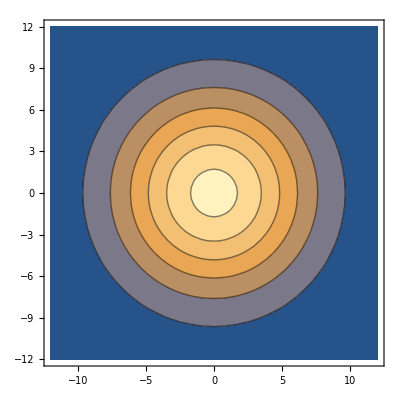

```mathematica
ContourPlot[f[x,y],{x,-12,12},{y,-12,12}]
```